```mathematica
ClearAll["Global`*"]
```

```mathematica
E1a[n_,k_, a_]:= E1a[n,k,a]=Sum[ E1a[n/j,k-1,a],{j,1,n}]-a Sum[ E1a[n/(a j),k-1,a],{j,1,n/a}];E1a[n_,0,a_]:=1
DDa[n_,k_]:=DDa[n,k]=Sum[DDa[Floor[n/j],k-1],{j,1,n}];DDa[n_,0]:=1
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
DDd[n_,z_]:=DDd[n,z]=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]
DDc[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j E1a[n/b^j, k, b],{j,0,Log[b,n]}]
E1c[n_,k_,b_]:=Sum[(-1)^j Binomial[k,j] b^j DDa[n/b^j,k],{j,0,k}]
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
E2z[n_,k_, a_]:= E2z[n,k,a]=Sum[ E2z[n/j,k-1,a],{j,2,n}]+a Sum[ E2z[n/(a j),k-1,a],{j,1,n/a}];E2z[n_,0,a_]:=1
E2r[n_,k_, a_]:= E2r[n,k,a]=Sum[ E2r[n/j,k-1,a],{j,2,n}]-Sum[ E2r[n/(a j),k-1,a],{j,1,n/a}];E2r[n_,0,a_]:=1
E2q[n_,k_, a_,b_]:= Sum[ E2q[n/j,k-1,a,b],{j,2,n}]-Sum[ E2q[n/(a j),k-1,a,b],{j,1,n/a}]-Sum[ E2q[n/(b j),k-1,a,b],{j,1,n/b}]
E2q[n_,0,a_,b_]:=1
Linr[ n_, a_] := Sum[ (-1)^(k+1)/k E2r[n,k,a],{k,1,Log[a,n]}]
Linq[ n_, a_,b_] := Sum[ (-1)^(k+1)/k E2q[n,k,a,b],{k,1,Log[a,n]}]
Linr2[ n_, a_] := Sum[ (-1)^(k+1)/k E2a[n,k,a],{k,1,Log[a,n]}]
Linz[ n_, a_] := Sum[ (-1)^(k+1)/k E2z[n,k,a],{k,1,Log[a,n]}]
```

```mathematica
DDa[100,1]
```

100

```mathematica
DDc[100,1,3]
```

100

```mathematica
fo[n_, k_, b_]:=DiscretePlot[{Binomial[k+j-1,k-1] b^j E1a[n/b^j, k, b]},{j,0,Log[b,n]}]
```

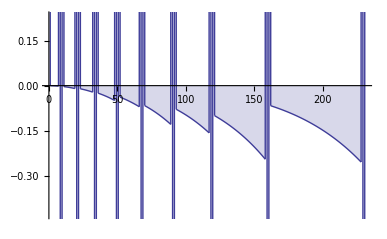

```mathematica
fo[10,3,1.01]
```

```mathematica
DDa[10,1]
```

10

```mathematica
DDc[10,1,.9]
```

0

```mathematica
E1a[10,2,.8]
```

-0.52

```mathematica
E1c[10,2,.8]
```

-0.2

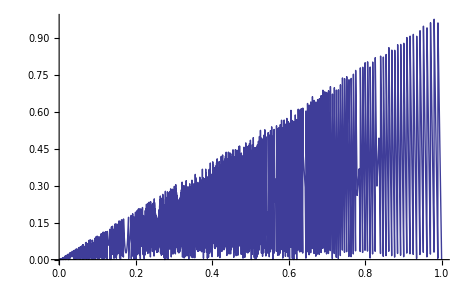

```mathematica
Plot[E1a[100,1,n],{n,0,1}]
```

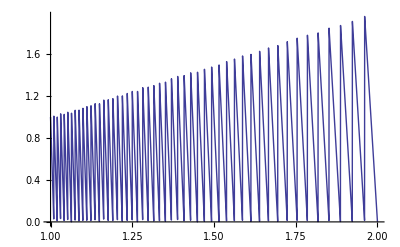

```mathematica
Plot[E1a[100,1,n],{n,1,2}]
```

```mathematica
E1a[10,1,.8]
```

0.4

```mathematica
-E1a[10,1,1/.8]
```

0.

```mathematica
N[Lin[10,1/2,13]]
```

-19.7409

```mathematica
Linr[100,2]+1+1/2+1/3+1/4+1/5+1/6
```

428/15

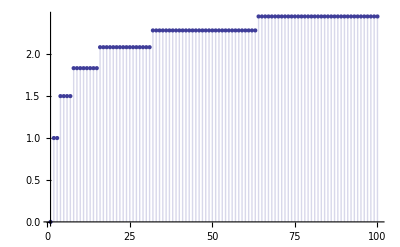

```mathematica
DiscretePlot[ Limit[ (DDd[n,z]-1)/z,z->0]-Linr[n,2],{n,1,100}]
```

```mathematica
Limit[ (DDd[100,z]-1)/z,z->0]
```

428/15

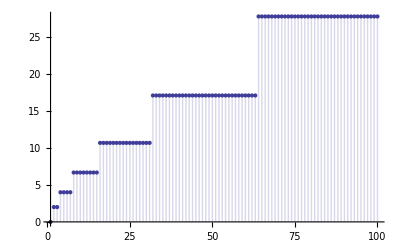

```mathematica
DiscretePlot[ Limit[ (DDd[n,z]-1)/z,z->0]-Linr2[n,2],{n,1,100}]
```

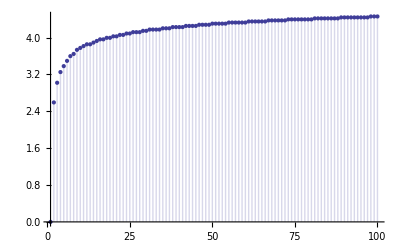

```mathematica
DiscretePlot[ Limit[ (DDd[n,z]-1)/z,z->0]-Linr[n,1.1],{n,1,100}]
```

```mathematica
ff[n_, a_, b_] := Sum[ 1/j,{j,1, Log[a,n]}]+Sum[ 1/j,{j,1, Log[b,n]}]-Sum[ 1/j,{j,1, Log[a b,n]}]
```

```mathematica
Linq[100,3,5]
```

251/12

```mathematica
Limit[ (DDd[100,z]-1)/z,z->0]-ff[100,3,5]
```

519/20

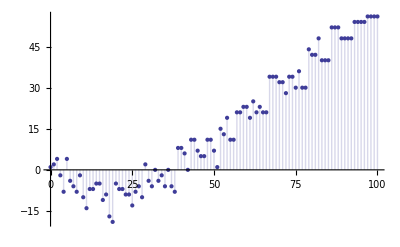

```mathematica
DiscretePlot[E2r[100,2,1+n/100],{n,0,100}]
```

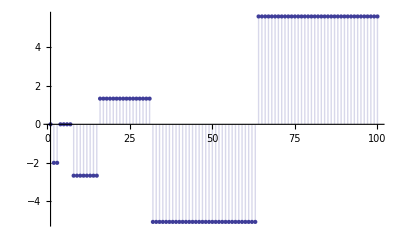

```mathematica
DiscretePlot[ Limit[ (DDd[n,z]-1)/z,z->0]-Linz[n,2],{n,1,100}]
```

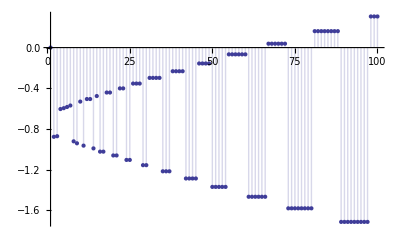

```mathematica
DiscretePlot[ Limit[ (DDd[n,z]-1)/z,z->0]-Linz[n,1.1],{n,1,100}]
```

```mathematica
fa[n_, a_ ]:= Sum[ (-1)^(k) a^k/k,{k,1,Log[a,n]}]
```

```mathematica
DiscretePlot[ fa[n,2],{n,1,100}]
```

-Graphics-

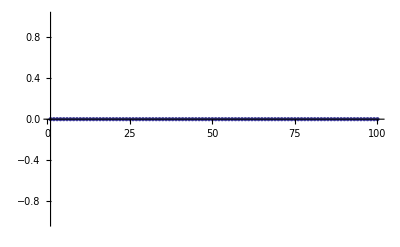

```mathematica
DiscretePlot[ Limit[ (DDd[n,z]-1)/z,z->0]-Linz[n,2] - fa[n,2],{n,1,100}]
```

```mathematica
Limit[Sum[ (-1)^(k) a^k/k,{k,1,Log[a,100]}],a->1]
```

Limit[100^(1+(ⅈ π)/Log[a]) a LerchPhi[-a,1,Log[100 a]/Log[a]]-Log[1+a],a→1]

```mathematica
fr[a_] := 100^(1+(ⅈ π)/Log[a]) a LerchPhi[-a,1,Log[100 a]/Log[a]]-Log[1+a]
```

```mathematica
fr[1.000001]
```

-0.693147+0.0000108508 ⅈ

```mathematica
N[-Log[2]]
```

-0.693147

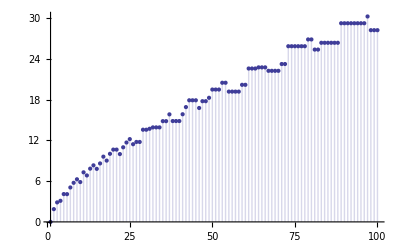

```mathematica
DiscretePlot[ Linz[n,1.1],{n,1,100}]
```

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Linz[100,1.05]
```

28.7193